# Omrežje in maksimalen tok

## Prvi primer

### CLP formulacija

Definirali bomo kapacitetno matriko omrežja in poiskali maksimalen tok. Primer n =4.

```mathematica
n=4
```

4

```mathematica
(mk={{0,5,7,0},{0,0,1,2},{0,6,0,9},{0,0,0,0}})//MatrixForm
```

(0 | 5 | 7 | 0
0 | 0 | 1 | 2
0 | 6 | 0 | 9
0 | 0 | 0 | 0)

Kapaciteta povezave v_i- v_j je k_ij. Vrednost toka od v_i do v_j je x_ij

```mathematica
var =Flatten[Table[Subscript[x, i,j],{i,n},{j,n}]]
```

{x_(1,1),x_(1,2),x_(1,3),x_(1,4),x_(2,1),x_(2,2),x_(2,3),x_(2,4),x_(3,1),x_(3,2),x_(3,3),x_(3,4),x_(4,1),x_(4,2),x_(4,3),x_(4,4)}

Vezi f_ij= x_ij≤ k_ijzapišemo matrično m.x≤ b. Desna stran

```mathematica
b= Partition[Riffle[Flatten[mk],Table[-1,{n^2}]],2]
```

{{0,-1},{5,-1},{7,-1},{0,-1},{0,-1},{0,-1},{1,-1},{2,-1},{0,-1},{6,-1},{0,-1},{9,-1},{0,-1},{0,-1},{0,-1},{0,-1}}

Matrika

```mathematica
m = IdentityMatrix[n^2];
```

Sedaj moramo dodati še ohranitvene pogoje za vse notranje vozle.

```mathematica
oz[i_]:= Sum[Subscript[x, i,j],{j,2,n}]-Sum[Subscript[x, j,i],{j,n-1}]
```

```mathematica
oz[2]
```

-x_(1,2)+x_(2,3)+x_(2,4)-x_(3,2)

Matrične koeficiente dobimo z CoefficientArrays

```mathematica
CoefficientArrays[oz[3],var][[2]]//Normal
```

{0,0,-1,0,0,0,-1,0,0,1,0,1,0,0,0,0}

Združimo vse vezi

```mathematica
(m=Join[m,Normal[{CoefficientArrays[oz[2],var][[2]],CoefficientArrays[oz[3],var][[2]]}]])//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0)

Združimo še desne strani

```mathematica
b= Join[b,Table[{0,0},{2}]]
```

{{0,-1},{5,-1},{7,-1},{0,-1},{0,-1},{0,-1},{1,-1},{2,-1},{0,-1},{6,-1},{0,-1},{9,-1},{0,-1},{0,-1},{0,-1},{0,-1},{0,0},{0,0}}

Vrednost toka je ∑_(j=1) x_(1j) . Tako je

```mathematica
c=Normal[CoefficientArrays[Sum[Subscript[x, 1,j],{j,2,n}],var][[2]]]
```

{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}

Rešimo LP

```mathematica
lp=LinearProgramming[-c,m,b]
```

{0,3,7,0,0,0,1,2,0,0,0,8,0,0,0,0}

Tok je

```mathematica
Partition[lp,n]//MatrixForm
```

(0 | 3 | 7 | 0
0 | 0 | 1 | 2
0 | 0 | 0 | 8
0 | 0 | 0 | 0)

Njegova vrednost ozirom moč pa

```mathematica
Sum[lp[[i]],{i,n}]
```

10

### Reševanje z ukazom FindMaximalFlow

Matriki mk priredimo graf

```mathematica
povezave= {};kapacitete = {};
Do[If[mk[[i,j]]≠ 0,
( AppendTo[povezave,i->j];
AppendTo[kapacitete,mk[[i,j]]])],{i,n},{j,n}]
povezave
kapacitete
```

{1->2,1->3,2->3,2->4,3->2,3->4}

{5,7,1,2,6,9}

```mathematica
vozlisca = Table[i,{i,n}]
```

{1,2,3,4}

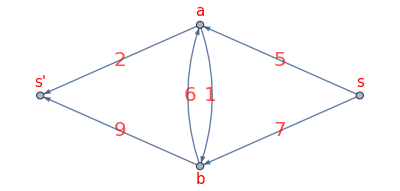

```mathematica
𝒢=Graph[vozlisca,povezave,EdgeCapacity->kapacitete,EdgeLabels-> Table[povezave[[i]]-> kapacitete[[i]],{i,Length[povezave]}],EdgeLabelStyle->Directive[Red,Italic,20],VertexLabels->{1->Placed["s",Above],2->Placed["a",Above],3->Placed["b",Below],4->Placed["s'",Above]},VertexLabelStyle->Directive[Red,Italic,15]]
```

```mathematica
ℱ=FindMaximumFlow[𝒢,1,4,"OptimumFlowData"];
ℱ["FlowValue"]
```

10

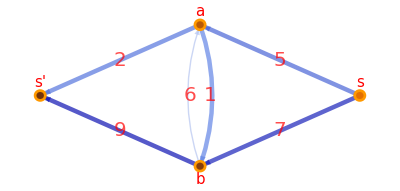

```mathematica
ℱ["FlowGraph"]
```

```mathematica
ℱ["FlowMatrix"]//MatrixForm
```

(0 | 3 | 7 | 0
0 | 0 | 1 | 2
0 | 0 | 0 | 8
0 | 0 | 0 | 0)

Dobili smo enak rezultat kot prej

```mathematica
#&/@ℱ["EdgeList"]
```

{1->2,1->3,2->3,2->4,3->4}

```mathematica
Grid[{#,ℱ[#]}&/@ℱ["EdgeList"],Frame->All,Alignment->Left]
```

1->2 | 3
1->3 | 7
2->3 | 1
2->4 | 2
3->4 | 8

## Drugi primer

### CLP formulacija

Naključni podatki

```mathematica
SeedRandom[121212]
```

```mathematica
n=10
```

10

```mathematica
(mk =Partition[Table[RandomInteger[{0,10}],{n^2}],n])//MatrixForm
```

(10 | 4 | 0 | 5 | 5 | 5 | 6 | 1 | 8 | 8
7 | 0 | 0 | 5 | 6 | 3 | 5 | 9 | 2 | 3
2 | 1 | 8 | 2 | 2 | 2 | 4 | 9 | 3 | 2
1 | 3 | 6 | 7 | 1 | 0 | 6 | 1 | 0 | 5
4 | 5 | 9 | 7 | 4 | 1 | 10 | 10 | 4 | 1
7 | 4 | 6 | 7 | 8 | 3 | 6 | 2 | 5 | 6
9 | 2 | 8 | 7 | 10 | 10 | 5 | 7 | 3 | 6
3 | 0 | 5 | 6 | 10 | 10 | 4 | 2 | 10 | 5
4 | 4 | 8 | 4 | 6 | 1 | 0 | 9 | 5 | 8
2 | 9 | 0 | 10 | 10 | 9 | 9 | 10 | 2 | 4)

```mathematica
Do[mk[[i,i]]= 0,{i,n}]
```

Kapaciteta povezave v_i- v_j je k_ij. Vrednost toka od v_i do v_j je x_ij

```mathematica
var =Flatten[Table[Subscript[x, i,j],{i,n},{j,n}]];
```

Vezi f_ij= x_ij≤ k_ijzapišemo matrično m.x≤ b. Desna stran

```mathematica
b= Partition[Riffle[Flatten[mk],Table[-1,{n^2}]],2];
```

Matrika

```mathematica
m = IdentityMatrix[n^2];
```

Sedaj moramo dodati še ohranitvene pogoje za vse notranje vozle.

```mathematica
oz[i_]:= Sum[Subscript[x, i,j],{j,2,n}]-Sum[Subscript[x, j,i],{j,n-1}]
```

Združimo vse vezi

```mathematica
m=Join[m,Normal[Table[CoefficientArrays[oz[k],var][[2]],{k,2,n-1}]]];
```

Združimo še desne strani

```mathematica
b= Join[b,Table[{0,0},{n-2}]];
```

Vrednost toka je ∑_(j=1) x_(1j) . Tako je

```mathematica
c=Normal[CoefficientArrays[Sum[Subscript[x, 1,j],{j,2,n}],var][[2]]]
```

{0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Rešimo LP

```mathematica
lp=LinearProgramming[-c,m,b]
```

{0,4,0,5,5,5,6,1,8,8,0,0,0,0,0,0,0,4,2,3,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,5,0,0,4,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,6,0,1,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,5,0,4,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0}

Tok je

```mathematica
Partition[lp,n]//MatrixForm
```

(0 | 4 | 0 | 5 | 5 | 5 | 6 | 1 | 8 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 3
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Njegova vrednost ozirom moč pa

```mathematica
Sum[lp[[i]],{i,n}]
```

42

### Reševanje z ukazom FindMaximalFlow

Matriki mk priredimo graf

```mathematica
Length[mk]
```

10

```mathematica
povezave= {};kapacitete = {};
Do[If[mk[[i,j]]≠ 0,
( AppendTo[povezave,i->j];
AppendTo[kapacitete,mk[[i,j]]])],{i,n},{j,n}]
```

```mathematica
oznakevozlisc =Join[ {1->Placed["s",Above],n->Placed["t",Above]},Table[k->Placed[Subscript["x", k],Above],{k,2,n-1}]]
```

{1→Placed[s,Above],10→Placed[t,Above],2→Placed[x_2,Above],3→Placed[x_3,Above],4→Placed[x_4,Above],5→Placed[x_5,Above],6→Placed[x_6,Above],7→Placed[x_7,Above],8→Placed[x_8,Above],9→Placed[x_9,Above]}

```mathematica
vozlisca=Table[i,{i,n}];
```

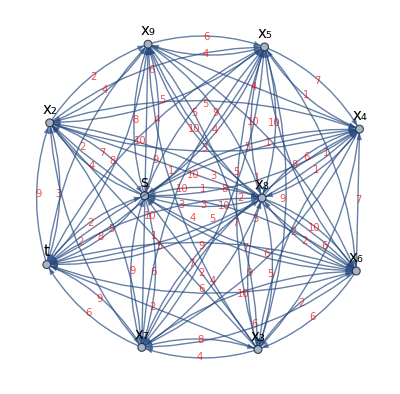

```mathematica
𝒢=Graph[vozlisca,povezave,EdgeCapacity->kapacitete,EdgeLabels-> Table[povezave[[i]]-> kapacitete[[i]],{i,Length[povezave]}],EdgeLabelStyle->Directive[Red,Italic,10],VertexLabels->oznakevozlisc,VertexLabelStyle->Directive[Black,Italic,15]]
```

```mathematica
ℱ=FindMaximumFlow[𝒢,1,n,"OptimumFlowData"];
ℱ["FlowValue"]
```

42

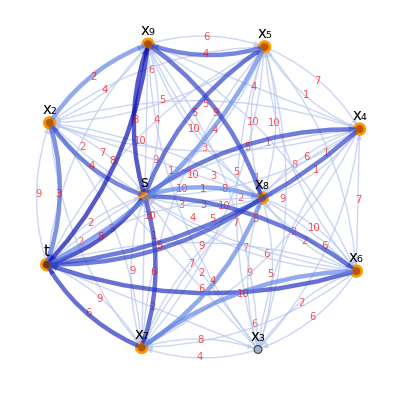

```mathematica
ℱ["FlowGraph"]
```

```mathematica
ℱ["FlowMatrix"]//MatrixForm
```

(0 | 4 | 0 | 5 | 5 | 5 | 6 | 1 | 8 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Dobili smo enako vrednost toka vendar drugi tok.

```mathematica
mk-Normal[ℱ["FlowMatrix"]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 5 | 6 | 3 | 5 | 9 | 1 | 0
2 | 1 | 0 | 2 | 2 | 2 | 4 | 9 | 3 | 2
1 | 3 | 6 | 0 | 1 | 0 | 6 | 1 | 0 | 0
4 | 5 | 9 | 7 | 0 | 1 | 10 | 10 | 0 | 0
7 | 4 | 6 | 7 | 8 | 0 | 6 | 2 | 5 | 0
9 | 2 | 8 | 7 | 10 | 9 | 0 | 7 | 3 | 0
3 | 0 | 5 | 6 | 10 | 10 | 3 | 0 | 10 | 0
4 | 4 | 8 | 4 | 6 | 1 | 0 | 4 | 0 | 0
2 | 9 | 0 | 10 | 10 | 9 | 9 | 10 | 2 | 0)

```mathematica
Grid[{#,ℱ[#]}&/@ℱ["EdgeList"],Frame->All,Alignment->Left]
```

1->2 | 4
1->4 | 5
1->5 | 5
1->6 | 5
1->7 | 6
1->8 | 1
1->9 | 8
1->10 | 8
2->9 | 1
2->10 | 3
4->10 | 5
5->9 | 4
5->10 | 1
6->10 | 6
7->6 | 1
7->10 | 6
8->7 | 1
8->10 | 5
9->8 | 5
9->10 | 8